```mathematica
γ=0.5772156649;
EA[x_]:=Log[x]+γ;
```

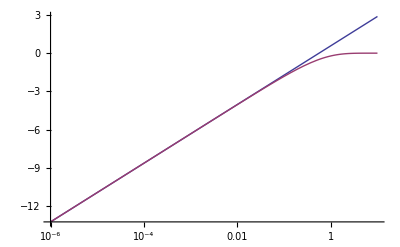

```mathematica
LogLinearPlot[{EA[x],ExpIntegralEi[-x]},{x,0.000001,10}]
```

```mathematica
rw=0.35;
μ=0.8;
ϕ=0.1;
k=10;
Export["expint.dat",Table[N[EA[x]],{x,{0.000001,0.000002,0.000003,0.000004,0.000005,0.000006,0.000007,0.000008,0.000009,0.00001,0.00002,0.00003,0.00004,0.00005,0.00006,0.00007,0.00008,0.00009,0.0001,0.0002,0.0003,0.0004,0.0005,0.0006,0.0007,0.0008,0.0009,0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,2,3,4,5,6,7,8,9,10
}}]]
```

expint.dat

```mathematica
N[ExpIntegralEi[-1]]
```

-0.219384

```mathematica
Export["expint.dat",Table[N[-0.5*ExpIntegralEi[-10^2/(4*t)]],{t,{0.01,0.01023293,0.010471285,0.010715193,0.010964782,0.011220185,0.011481536,0.011748976,0.012022644,0.012302688,0.012589254,0.012882496,0.013182567,0.013489629,0.013803843,0.014125375,0.014454398,0.014791084,0.015135612,0.015488166,0.015848932,0.016218101,0.016595869,0.016982437,0.017378008,0.017782794,0.018197009,0.018620871,0.019054607,0.019498446,0.019952623,0.020417379,0.020892961,0.021379621,0.021877616,0.022387211,0.022908677,0.023442288,0.023988329,0.024547089,0.025118864,0.025703958,0.02630268,0.026915348,0.027542287,0.028183829,0.028840315,0.029512092,0.030199517,0.030902954,0.031622777,0.032359366,0.033113112,0.033884416,0.034673685,0.035481339,0.036307805,0.037153523,0.03801894,0.038904514,0.039810717,0.040738028,0.041686938,0.042657952,0.043651583,0.044668359,0.045708819,0.046773514,0.047863009,0.048977882,0.050118723,0.051286138,0.052480746,0.05370318,0.054954087,0.056234133,0.057543994,0.058884366,0.060255959,0.0616595,0.063095734,0.064565423,0.066069345,0.067608298,0.069183097,0.070794578,0.072443596,0.074131024,0.075857758,0.077624712,0.079432823,0.081283052,0.083176377,0.085113804,0.087096359,0.089125094,0.091201084,0.09332543,0.095499259,0.097723722,0.1,0.102329299,0.104712855,0.107151931,0.10964782,0.112201845,0.114815362,0.117489755,0.120226443,0.123026877,0.125892541,0.128824955,0.131825674,0.134896288,0.138038426,0.141253754,0.144543977,0.147910839,0.151356125,0.154881662,0.158489319,0.16218101,0.165958691,0.169824365,0.173780083,0.177827941,0.181970086,0.186208714,0.190546072,0.19498446,0.199526231,0.204173794,0.208929613,0.213796209,0.218776162,0.223872114,0.229086765,0.234422882,0.239883292,0.245470892,0.251188643,0.257039578,0.263026799,0.26915348,0.27542287,0.281838293,0.28840315,0.295120923,0.301995172,0.309029543,0.316227766,0.323593657,0.331131121,0.338844156,0.34673685,0.354813389,0.363078055,0.371535229,0.380189396,0.389045145,0.398107171,0.407380278,0.416869383,0.426579519,0.436515832,0.446683592,0.45708819,0.467735141,0.478630092,0.489778819,0.501187234,0.512861384,0.52480746,0.537031796,0.549540874,0.562341325,0.575439937,0.588843655,0.602559586,0.616595002,0.630957344,0.645654229,0.660693448,0.676082975,0.691830971,0.707945784,0.72443596,0.741310241,0.758577575,0.776247117,0.794328235,0.812830516,0.831763771,0.851138038,0.87096359,0.891250938,0.912010839,0.933254301,0.954992586,0.977237221,1,1.023292992,1.047128548,1.071519305,1.096478196,1.122018454,1.148153622,1.174897555,1.202264435,1.230268771,1.258925412,1.288249552,1.318256739,1.348962883,1.380384265,1.412537545,1.445439771,1.479108388,1.513561248,1.548816619,1.584893192,1.621810097,1.659586907,1.698243652,1.737800829,1.77827941,1.819700859,1.862087137,1.905460718,1.9498446,1.995262315,2.041737945,2.089296131,2.13796209,2.187761624,2.238721139,2.290867653,2.344228815,2.398832919,2.454708916,2.511886432,2.570395783,2.630267992,2.691534804,2.754228703,2.818382931,2.884031503,2.951209227,3.01995172,3.090295433,3.16227766,3.235936569,3.311311215,3.388441561,3.467368505,3.548133892,3.630780548,3.715352291,3.801893963,3.89045145,3.981071706,4.073802778,4.168693835,4.265795188,4.365158322,4.466835922,4.570881896,4.677351413,4.786300923,4.897788194,5.011872336,5.12861384,5.248074603,5.370317964,5.495408739,5.623413252,5.754399373,5.888436554,6.025595861,6.165950019,6.309573445,6.45654229,6.60693448,6.760829754,6.918309709,7.079457844,7.244359601,7.413102413,7.58577575,7.762471166,7.943282347,8.128305162,8.317637711,8.511380382,8.7096359,8.912509381,9.120108394,9.332543008,9.54992586,9.77237221,10,10.23292992,10.47128548,10.71519305,10.96478196,11.22018454,11.48153622,11.74897555,12.02264435,12.30268771,12.58925412,12.88249552,13.18256739,13.48962883,13.80384265,14.12537545,14.45439771,14.79108388,15.13561248,15.48816619,15.84893192,16.21810097,16.59586907,16.98243652,17.37800829,17.7827941,18.19700859,18.62087137,19.05460718,19.498446,19.95262315,20.41737945,20.89296131,21.3796209,21.87761624,22.38721139,22.90867653,23.44228815,23.98832919,24.54708916,25.11886432,25.70395783,26.30267992,26.91534804,27.54228703,28.18382931,28.84031503,29.51209227,30.1995172,30.90295433,31.6227766,32.35936569,33.11311215,33.88441561,34.67368505,35.48133892,36.30780548,37.15352291,38.01893963,38.9045145,39.81071706,40.73802778,41.68693835,42.65795188,43.65158322,44.66835922,45.70881896,46.77351413,47.86300923,48.97788194,50.11872336,51.2861384,52.48074603,53.70317964,54.95408739,56.23413252,57.54399373,58.88436554,60.25595861,61.65950019,63.09573445,64.5654229,66.0693448,67.60829754,69.18309709,70.79457844,72.44359601,74.13102413,75.8577575,77.62471166,79.43282347,81.28305162,83.17637711,85.11380382,87.096359,89.12509381,91.20108394,93.32543008,95.4992586,97.7237221,100,102.3292992,104.7128548,107.1519305,109.6478196,112.2018454,114.8153622,117.4897555,120.2264435,123.0268771,125.8925412,128.8249552,131.8256739,134.8962883,138.0384265,141.2537545,144.5439771,147.9108388,151.3561248,154.8816619,158.4893192,162.1810097,165.9586907,169.8243652,173.7800829,177.827941,181.9700859,186.2087137,190.5460718,194.98446,199.5262315,204.1737945,208.9296131,213.796209,218.7761624,223.8721139,229.0867653,234.4228815,239.8832919,245.4708916,251.1886432,257.0395783,263.0267992,269.1534804,275.4228703,281.8382931,288.4031503,295.1209227,301.995172,309.0295433,316.227766,323.5936569,331.1311215,338.8441561,346.7368505,354.8133892,363.0780548,371.5352291,380.1893963,389.045145,398.1071706,407.3802778,416.8693835,426.5795188,436.5158322,446.6835922,457.0881896,467.7351413,478.6300923,489.7788194,501.1872336,512.861384,524.8074603,537.0317964,549.5408739,562.3413252,575.4399373,588.8436554,602.5595861,616.5950019,630.9573445,645.654229,660.693448,676.0829754,691.8309709,707.9457844,724.4359601,741.3102413,758.577575,776.2471166,794.3282347,812.8305162,831.7637711,851.1380382,870.96359,891.2509381,912.0108394,933.2543008,954.992586,977.237221,1000
}}]]
```

expint.dat

```mathematica
pD[rD_,tD_]:=-2/π*NIntegrate[((1-ⅇ^(-u^2*tD))*(BesselJ[0,u*rD]*BesselY[1,u]-BesselY[0,u*rD]*BesselJ[1,u])/(u^2*(BesselJ[1,u]*BesselJ[1,u]+BesselY[1,u]*BesselY[1,u]))),{u,0,100000},PrecisionGoal->50]
```

```mathematica
Export["FiniteWellbore_rD=20.dat",Table[N[-2/π*NIntegrate[((1-ⅇ^(-u^2*t))*(BesselJ[0,u*20]*BesselY[1,u]-BesselY[0,u*20]*BesselJ[1,u])/(u^2*(BesselJ[1,u]*BesselJ[1,u]+BesselY[1,u]*BesselY[1,u]))),{u,0,100}]],{t,{0.01,0.01023293,0.010471285,0.010715193,0.010964782,0.011220185,0.011481536,0.011748976,0.012022644,0.012302688,0.012589254,0.012882496,0.013182567,0.013489629,0.013803843,0.014125375,0.014454398,0.014791084,0.015135612,0.015488166,0.015848932,0.016218101,0.016595869,0.016982437,0.017378008,0.017782794,0.018197009,0.018620871,0.019054607,0.019498446,0.019952623,0.020417379,0.020892961,0.021379621,0.021877616,0.022387211,0.022908677,0.023442288,0.023988329,0.024547089,0.025118864,0.025703958,0.02630268,0.026915348,0.027542287,0.028183829,0.028840315,0.029512092,0.030199517,0.030902954,0.031622777,0.032359366,0.033113112,0.033884416,0.034673685,0.035481339,0.036307805,0.037153523,0.03801894,0.038904514,0.039810717,0.040738028,0.041686938,0.042657952,0.043651583,0.044668359,0.045708819,0.046773514,0.047863009,0.048977882,0.050118723,0.051286138,0.052480746,0.05370318,0.054954087,0.056234133,0.057543994,0.058884366,0.060255959,0.0616595,0.063095734,0.064565423,0.066069345,0.067608298,0.069183097,0.070794578,0.072443596,0.074131024,0.075857758,0.077624712,0.079432823,0.081283052,0.083176377,0.085113804,0.087096359,0.089125094,0.091201084,0.09332543,0.095499259,0.097723722,0.1,0.102329299,0.104712855,0.107151931,0.10964782,0.112201845,0.114815362,0.117489755,0.120226443,0.123026877,0.125892541,0.128824955,0.131825674,0.134896288,0.138038426,0.141253754,0.144543977,0.147910839,0.151356125,0.154881662,0.158489319,0.16218101,0.165958691,0.169824365,0.173780083,0.177827941,0.181970086,0.186208714,0.190546072,0.19498446,0.199526231,0.204173794,0.208929613,0.213796209,0.218776162,0.223872114,0.229086765,0.234422882,0.239883292,0.245470892,0.251188643,0.257039578,0.263026799,0.26915348,0.27542287,0.281838293,0.28840315,0.295120923,0.301995172,0.309029543,0.316227766,0.323593657,0.331131121,0.338844156,0.34673685,0.354813389,0.363078055,0.371535229,0.380189396,0.389045145,0.398107171,0.407380278,0.416869383,0.426579519,0.436515832,0.446683592,0.45708819,0.467735141,0.478630092,0.489778819,0.501187234,0.512861384,0.52480746,0.537031796,0.549540874,0.562341325,0.575439937,0.588843655,0.602559586,0.616595002,0.630957344,0.645654229,0.660693448,0.676082975,0.691830971,0.707945784,0.72443596,0.741310241,0.758577575,0.776247117,0.794328235,0.812830516,0.831763771,0.851138038,0.87096359,0.891250938,0.912010839,0.933254301,0.954992586,0.977237221,1,1.023292992,1.047128548,1.071519305,1.096478196,1.122018454,1.148153622,1.174897555,1.202264435,1.230268771,1.258925412,1.288249552,1.318256739,1.348962883,1.380384265,1.412537545,1.445439771,1.479108388,1.513561248,1.548816619,1.584893192,1.621810097,1.659586907,1.698243652,1.737800829,1.77827941,1.819700859,1.862087137,1.905460718,1.9498446,1.995262315,2.041737945,2.089296131,2.13796209,2.187761624,2.238721139,2.290867653,2.344228815,2.398832919,2.454708916,2.511886432,2.570395783,2.630267992,2.691534804,2.754228703,2.818382931,2.884031503,2.951209227,3.01995172,3.090295433,3.16227766,3.235936569,3.311311215,3.388441561,3.467368505,3.548133892,3.630780548,3.715352291,3.801893963,3.89045145,3.981071706,4.073802778,4.168693835,4.265795188,4.365158322,4.466835922,4.570881896,4.677351413,4.786300923,4.897788194,5.011872336,5.12861384,5.248074603,5.370317964,5.495408739,5.623413252,5.754399373,5.888436554,6.025595861,6.165950019,6.309573445,6.45654229,6.60693448,6.760829754,6.918309709,7.079457844,7.244359601,7.413102413,7.58577575,7.762471166,7.943282347,8.128305162,8.317637711,8.511380382,8.7096359,8.912509381,9.120108394,9.332543008,9.54992586,9.77237221,10,10.23292992,10.47128548,10.71519305,10.96478196,11.22018454,11.48153622,11.74897555,12.02264435,12.30268771,12.58925412,12.88249552,13.18256739,13.48962883,13.80384265,14.12537545,14.45439771,14.79108388,15.13561248,15.48816619,15.84893192,16.21810097,16.59586907,16.98243652,17.37800829,17.7827941,18.19700859,18.62087137,19.05460718,19.498446,19.95262315,20.41737945,20.89296131,21.3796209,21.87761624,22.38721139,22.90867653,23.44228815,23.98832919,24.54708916,25.11886432,25.70395783,26.30267992,26.91534804,27.54228703,28.18382931,28.84031503,29.51209227,30.1995172,30.90295433,31.6227766,32.35936569,33.11311215,33.88441561,34.67368505,35.48133892,36.30780548,37.15352291,38.01893963,38.9045145,39.81071706,40.73802778,41.68693835,42.65795188,43.65158322,44.66835922,45.70881896,46.77351413,47.86300923,48.97788194,50.11872336,51.2861384,52.48074603,53.70317964,54.95408739,56.23413252,57.54399373,58.88436554,60.25595861,61.65950019,63.09573445,64.5654229,66.0693448,67.60829754,69.18309709,70.79457844,72.44359601,74.13102413,75.8577575,77.62471166,79.43282347,81.28305162,83.17637711,85.11380382,87.096359,89.12509381,91.20108394,93.32543008,95.4992586,97.7237221,100,102.3292992,104.7128548,107.1519305,109.6478196,112.2018454,114.8153622,117.4897555,120.2264435,123.0268771,125.8925412,128.8249552,131.8256739,134.8962883,138.0384265,141.2537545,144.5439771,147.9108388,151.3561248,154.8816619,158.4893192,162.1810097,165.9586907,169.8243652,173.7800829,177.827941,181.9700859,186.2087137,190.5460718,194.98446,199.5262315,204.1737945,208.9296131,213.796209,218.7761624,223.8721139,229.0867653,234.4228815,239.8832919,245.4708916,251.1886432,257.0395783,263.0267992,269.1534804,275.4228703,281.8382931,288.4031503,295.1209227,301.995172,309.0295433,316.227766,323.5936569,331.1311215,338.8441561,346.7368505,354.8133892,363.0780548,371.5352291,380.1893963,389.045145,398.1071706,407.3802778,416.8693835,426.5795188,436.5158322,446.6835922,457.0881896,467.7351413,478.6300923,489.7788194,501.1872336,512.861384,524.8074603,537.0317964,549.5408739,562.3413252,575.4399373,588.8436554,602.5595861,616.5950019,630.9573445,645.654229,660.693448,676.0829754,691.8309709,707.9457844,724.4359601,741.3102413,758.577575,776.2471166,794.3282347,812.8305162,831.7637711,851.1380382,870.96359,891.2509381,912.0108394,933.2543008,954.992586,977.237221,1000
}}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.837491664053238`}. NIntegrate obtained -7.29351×10^-7 and 3.28594×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.837491664053238`}. NIntegrate obtained -7.29351×10^-7 and 3.32415×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {6.837491664053238`}. NIntegrate obtained -7.29351×10^-7 and 3.36195×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

FiniteWellbore_rD=20.dat

```mathematica
ⅇ^0.80907
```

2.24582

```mathematica
Log[0.0002637]+0.8097
```

```mathematica
-7.430998464605033/2
```

```mathematica
-3.7154992323025167*0.43429448190325176
```

-1.61362

```mathematica
3.23*1.151
```

3.71773

```mathematica
0.43429448190325176*2
```

0.868589

```mathematica
4/ⅇ^0.577215665
```

2.24584

```mathematica
N[Log[10,ⅇ]]*Log[4/ⅇ^0.57721566490]
```

0.351378

```mathematica
N[1/(2*Log[10,ⅇ])]
```

1.15129